# QEdark-f2 analysis

Change log
v3: 
Jan 22, 2021
added note about prefactors wk/2*wk/2*1/wk in the definition of e.g. dRdESi 
July 18, 2019
changed input file names from C.Si.137.dat to Si_f2.dat and C.Ge.137.dat to Ge_f2.dat
fixed implementation of σetest

v2: Updated June 14, 2019
Changes: 
- definition of electron mass and speed of light (me -> meeV, c -> ccms)
- removed redundant mass dependence in σetest
- fixed table for plotting  dRdESi to include binsize normalization
- fixed table for plotting dRdESi to have  Emin=Egap instead of Emin=0

set working directories

```mathematica
MyDirectory="My/Working/Directory/";(* working directory where files are stored *)
PlotDir=MyDirectory<>"plots/";
```

load factor files

### Import data

```mathematica
(*in 900 bins of Δq=0.02 α Subscript[m, e] and 500 E bins of ΔE=0.1 eV*)
rawFFdataSi=Import[MyDirectory<>"Si_f2.dat","table"];
rawFFdataGe=Import[MyDirectory<>"Ge_f2.dat","table"];
```

```mathematica
(* put into square arrays: E across, q down*)
FFarraySi=Block[{Nqbins=900,NEbins=500},
ArrayReshape[rawFFdataSi,{NEbins,Nqbins}]]//Transpose;
FFarrayGe=Block[{Nqbins=900,NEbins=500},
ArrayReshape[rawFFdataGe,{NEbins,Nqbins}]]//Transpose;

(*Binning: 500 E bins of  ΔE = 0.1 eV = 0.1/13.6 Subscript[R, y] × 900 bins of  Δq = 0.02 αme *)
```

unit conversions and constants

```mathematica
sec2year=60*60*24*365.25;
amu2kg=1.660538782 10^-27;
α=1/137.; (* fine structure constant *)
meeV=0.511 10^6; (* electron mass [eV] *)
ρχ=0.4 10^9; (* local DM density [eV/cm^3] *)
```

```mathematica
ccms=2.99792458 10^10; (* speed of light [cm/s] *)
v0=230 10^5; (* typical velocity [cm/s] *)
vE = 240 10^5; (* velocity of Earth [cm/s] *)
vesc=600 10^5; (* escape velocity [cm/s] *)
KK=v0^3(-2. Exp[-vesc^2/v0^2]π vesc/v0+π^(3/2)Erf[vesc/v0]) (* [cm/s]^3*);
```

velocity distribution and F_DM definition

```mathematica
vmin[q_?NumberQ,Ee_?NumberQ,mχ_?NumberQ]:=ccms(q/(2 mχ)+Ee/q);
```

```mathematica
(* Maxwell-Boltzmann distribution 
η(Subscript[v, min])=∫(d^3 v)/v Subscript[f, MB](v)θ(v-Subscript[v, min])
*)
η[q_?NumberQ,Ee_?NumberQ,mχ_?NumberQ]:=(v0^2 π)/(2 vE KK)*Piecewise[{{-4 Exp[-vesc^2/v0^2]vE+√π v0(Erf[(vmin[q,Ee,mχ]+vE)/v0]-Erf[(vmin[q,Ee,mχ]-vE)/v0]),vmin[q,Ee,mχ]<vesc-vE},{-2 Exp[-vesc^2/v0^2](vE+vesc-vmin[q,Ee,mχ])+√π v0(Erf[vesc/v0]-Erf[(vmin[q,Ee,mχ]-vE)/v0]),vmin[q,Ee,mχ]<vesc+vE&&vesc-vE<vmin[q,Ee,mχ]},{0,vmin[q,Ee,mχ]>vesc+vE}}]
```

```mathematica
FDM[q_?NumberQ,n_?NumberQ]:=((α meeV)/q)^n
```

Rate

```mathematica
μχe[mχ_]:=(meeV mχ)/(meeV+ mχ);
σetest=1. 10^-37; (* cm^2*)
```

## Si

dRdESi is equivalent to (3.13)

```mathematica
(* Subscript[f, crystal]=(...) Eq. (4.4) *)
(* ATTENTION: if you use C.137.dat from the QEdark website, use the following code. If you generate your own f2 files from the code, please remove the term wk/2 wk/2 1/wk as it is encoded in the QEdark output *)

dRdESi[mχ_,EE_?NumberQ,n_?NumberQ]:=With[{qunit=0.02 α meeV(* eV *),Eunit=0.1(* eV *),Eprefactor=2.0 (* eV *),wk=2/137,MTarget=1 (*kg*),MCell=2*28.0855 amu2kg},  ccms^2 sec2year ρχ/mχ MTarget/MCell σetest (α meeV^2)/μχe[mχ]^2 Sum[Eunit qunit 1/(qi*qunit)η[qi*qunit,EE  ,mχ] FDM[qi*qunit,n]^2(Eprefactor 1/qunit 1/Eunit wk/2 wk/2 1/wk FFarraySi[[qi,Floor[EE/Eunit]]]),{qi,1,900}]]
```

```mathematica
RateSi[mχ_ (* MeV *),Emin_,n_]:=With[{Eunit=0.1},Sum[ dRdESi[mχ 10^6,EE,n],{EE,Emin,500 Eunit,Eunit}]]
```

### plot dR/dE

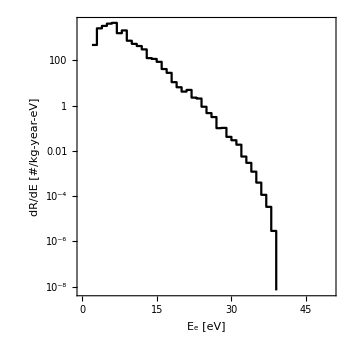

```mathematica
With[{binsize=1.,Egap=1.1,Eunit=0.1,mχ=10. 10^6 (* eV *),iiFDM=0 (* FDM=1 *)},
tmptable=Table[{EE,binsize dRdESi[mχ,EE,iiFDM]},{EE,Egap,50,binsize}];myf2SiPlot=ListLogPlot[tmptable,Joined->True,PlotRange->{{0,50},All},InterpolationOrder->0,PlotStyle->Black,Frame->True,FrameLabel->{"E_e [eV]","dR/dE [#/kg-year-eV]","(σ̄)_e= 10^-37 [cm^2], F_DM(q)=1, mχ="<>ToString[mχ/10^6]<>" MeV"}]]
```

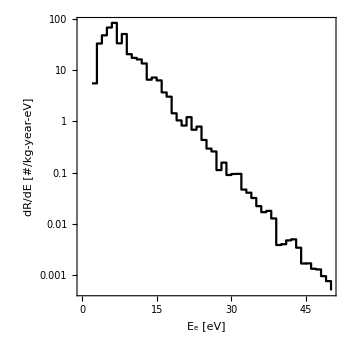

```mathematica
With[{binsize=1.,Egap=1.1,Eunit=0.1,mχ=1. 10^9 (* eV *),iiFDM=0 (* FDM=1 *)},
tmptable=Table[{EE,binsize dRdESi[mχ,EE,iiFDM]},{EE,Egap,50,binsize}];myf2SiPlot=ListLogPlot[tmptable,Joined->True,PlotRange->{{0,50},All},InterpolationOrder->0,PlotStyle->Black,Frame->True,FrameLabel->{"E_e [eV]","dR/dE [#/kg-year-eV]","(σ̄)_e= 10^-37 [cm^2], F_DM(q)=1, mχ="<>ToString[mχ/10^6]<>" MeV"}]]
```

### calculate rate and (σ̄)_e (* n.b. each mass takes ~100s to run for E_min=E_gap*)

```mathematica
nevents=3.6; (* events observed *)
years=1; (*exposure in years. 365.25 days = 1 year*)
kg=1.0; (* detector size in kg *)
exposure=years*kg;
```

```mathematica
With[{mX=10.,Emin=1.1,n=0},
tmp=RateSi[mX ,Emin,n];
Print["Rate = ",tmp," events/kg/year"];
Print["For m_χ = ",mX," MeV, (σ̄)_e=",nevents/(tmp*exposure)σetest[mχ]," cm^2"] ]
```

Rate = 203213. events/kg/year

For m_χ = 10. MeV, (σ̄)_e=1.77154×10^-42 cm^2

```mathematica
With[{mX=1000.,Emin=1.1,n=0},
tmp=RateSi[mX ,Emin,n];
Print["Rate = ",tmp," events/kg/year"];
Print["For m_χ = ",mX," MeV, (σ̄)_e=",nevents/(tmp*exposure)σetest[mχ]," cm^2"] ]
```

Rate = 4159.3 events/kg/year

For m_χ = 1000. MeV, (σ̄)_e=8.65531×10^-41 cm^2

```mathematica
tmpSiTable=With[{Emin=1.1,n=0},Table[{mX,nevents/(RateSi[mX ,Emin,n]*exposure)10^-37},{mX,{0.1,0.5,1.0,2.0,3.0,5.0,7.0,10.,20.,50.,1000.}}]];
```

Power::infy: Infinite expression 1/0. encountered.

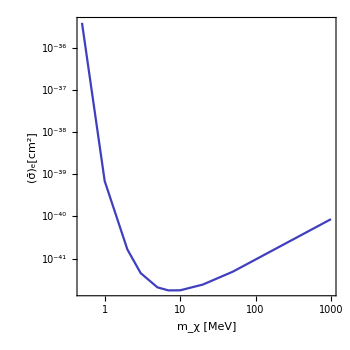

```mathematica
ListLogLogPlot[tmpSiTable,PlotStyle->Blend[{Blue,Gray}],FrameLabel->{"m_χ [MeV]","(σ̄)_e[cm^2]"}]
```

## Ge

dRdEGe is equivalent to (3.13)

```mathematica
(* Subscript[f, crystal]=(...) Eq. (4.4) *)
(* ATTENTION: if you use C.137.dat from the QEdark website, use the following code. If you generate your own f2 files from the code, please remove the term wk/2 wk/2 1/wk as it is encoded in the QEdark output *)

dRdEGe[mχ_,EE_?NumberQ,n_?NumberQ]:=With[{qunit=0.02 α meeV(* eV *),Eunit=0.1(* eV *),Eprefactor=1.8 (* eV *),wk=2/137,MTarget=1 (*kg*),MCell=2*72.64 amu2kg},  ccms^2 sec2year ρχ/mχ MTarget/MCell σetest (α meeV^2)/μχe[mχ]^2 Sum[Eunit qunit 1/(qi*qunit)η[qi*qunit,EE  ,mχ] FDM[qi*qunit,n]^2(Eprefactor 1/qunit 1/Eunit wk/2 wk/2 1/wk FFarrayGe[[qi,Floor[EE/Eunit]]]),{qi,1,900}]]
```

```mathematica
RateGe[mχ_ (* MeV *),Emin_,n_]:=With[{Eunit=0.1},Sum[ dRdEGe[mχ 10^6,EE,n],{EE,Emin,500 Eunit,Eunit}]]
```

### plot dR/dE

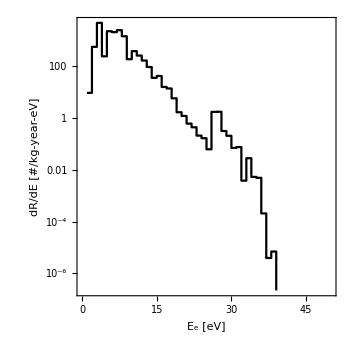

```mathematica
With[{binsize=1.,Egap=0.7 (* eV *),mχ=10. 10^6 (* eV *),iiFDM=0 (* FDM=1 *)},
tmptable=Table[{EE,binsize dRdEGe[mχ,EE,iiFDM]},{EE,Egap,50,binsize}];myf2GePlot=ListLogPlot[tmptable,Joined->True,PlotRange->{{0,50},All},InterpolationOrder->0,PlotStyle->Black,Frame->True,FrameLabel->{"E_e [eV]","dR/dE [#/kg-year-eV]","(σ̄)_e= 10^-37 [cm^2], F_DM(q)=1, mχ="<>ToString[mχ/10^6]<>" MeV"}]]
```

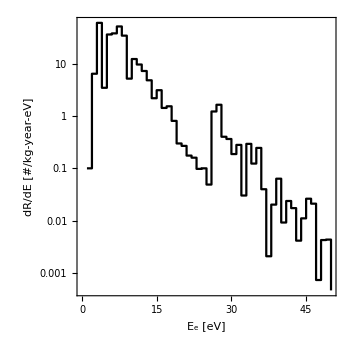

```mathematica
With[{binsize=1.,mχ=1. 10^9 (* eV *),Egap=0.7 (*eV*),iiFDM=0 (* FDM=1 *)},
tmptable=Table[{EE,binsize dRdEGe[mχ,EE,iiFDM]},{EE,0,50,binsize}];myf2GePlot=ListLogPlot[tmptable,Joined->True,PlotRange->{{0,50},All},InterpolationOrder->0,PlotStyle->Black,Frame->True,FrameLabel->{"E_e [eV]","dR/dE [#/kg-year-eV]","(σ̄)_e= 10^-37 [cm^2], F_DM(q)=1, mχ="<>ToString[mχ/10^6]<>" MeV"}]]
```

### calculate rate and (σ̄)_e (* n.b. each mass takes ~100s to run for E_min=E_gap*)

```mathematica
nevents=3.0; (* events observed *)
years=1; (*exposure in years. 365.25 days = 1 year*)
kg=1.0; (* detector size in kg *)
exposure=years*kg;
```

```mathematica
With[{mX=10.,Emin=0.67,n=0},
tmp=RateGe[mX ,Emin,n];
Print["Rate = ",tmp," events/kg/year"];
Print["For m_χ = ",mX," MeV, (σ̄)_e=",nevents/(tmp *exposure)σetest[mχ]," cm^2"]]
```

Rate = 67858.5 events/kg/year

For m_χ = 10. MeV, (σ̄)_e=5.30516×10^-42 cm^2

```mathematica
With[{mX=1000.,Emin=0.67,n=0},
tmp=RateGe[mX ,Emin,n];
Print["Rate = ",tmp," events/kg/year"];
Print["For m_χ = ",mX," MeV, (σ̄)_e=",nevents/(tmp*exposure)σetest[mχ]," cm^2"]
]
```

Rate = 1324.12 events/kg/year

For m_χ = 1000. MeV, (σ̄)_e=2.71878×10^-40 cm^2

```mathematica
tmpGeTable=With[{Emin=0.67,n=0},Table[{mX,nevents/(RateGe[mX ,Emin,n]*exposure)σetest[mX]},{mX,{0.1,0.5,1.0,2.0,3.0,5.0,7.0,10.,20.,50.,1000.}}]];
```

Power::infy: Infinite expression 1/0. encountered.

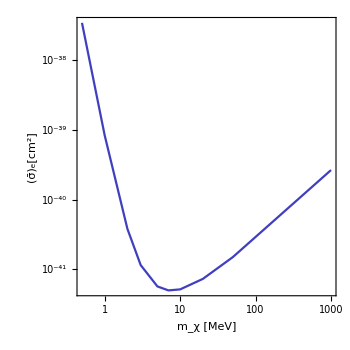

```mathematica
ListLogLogPlot[tmpGeTable,PlotStyle->Blend[{Blue,Gray}],FrameLabel->{"m_χ [MeV]","(σ̄)_e[cm^2]"}]
```